# Расчёт заселённостей в модели Больцмана

Пользуясь Q определим заселённость iго уровня P_i

```mathematica
popul[i_]:=Exp[(-Subscript[ε, i])/(k T)]/Q
```

## Гармонический осциллятор

Под энергией ε_i будем понимать энергию гармонического осциллятора

```mathematica
Subscript[ε, n_]:=h c ω n
```

Зададим выражение для статсуммы Q

```mathematica
Q=∑_(n=0)^∞ Exp[(-Subscript[ε, n])/(k T)]
```

ⅇ^((c h ω)/(k T))/(-1+ⅇ^((c h ω)/(k T)))

Тогда выражение для заселённостей упростится

```mathematica
populHarm=popul[i]//Simplify
```

ⅇ^(-(c h (1+i) ω)/(k T)) (-1+ⅇ^((c h ω)/(k T)))

Явно выделим характеристическую температуру θ

```mathematica
populHarm=populHarm/.(h c ω)/k->θ
```

ⅇ^(-((1+i) θ)/T) (-1+ⅇ^(θ/T))

Заменим T/θ на приведённую температуру T_red

```mathematica
populHarm=populHarm/.θ/T->1/Tred
```

ⅇ^(-(1+i)/Tred) (-1+ⅇ^(1/Tred))

Найдём выражения для первых 4х уровней (i = 0, 1, 2, 3)

```mathematica
levelsHarm=Table[populHarm,{i,0,3}]
```

{ⅇ^(-1/Tred) (-1+ⅇ^(1/Tred)),ⅇ^(-2/Tred) (-1+ⅇ^(1/Tred)),ⅇ^(-3/Tred) (-1+ⅇ^(1/Tred)),ⅇ^(-4/Tred) (-1+ⅇ^(1/Tred))}

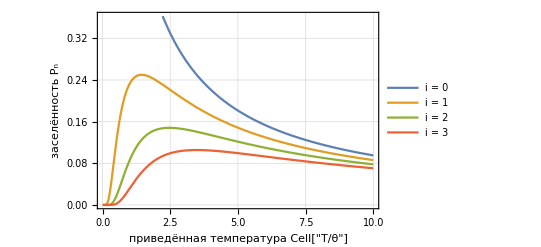

```mathematica
Plot[levelsHarm,{Tred,0.01,10},
PlotTheme->"Detailed",PlotLegends->Map[StringTemplate["i = ``"],Range[0,3]],
FrameLabel->{"приведённая температура Cell["T/θ",ExpressionUUID->"73dc71cc-baed-4396-a014-9de7d23da820"]","заселённость P_n"}
]
```

Найдём выражение для средней энергии ⟨ε⟩

```mathematica
meanEHarm=∑_(i=0)^∞ populHarm Subscript[ε, i]
```

(c h ω)/(-1+ⅇ^(1/Tred))

полученное выражение явным образом зависит от колебательной частоты ω (или, что то же самое, от разности энергии Δε между уровнями), для определённости сократим на эту величину и получим приведённую среднюю энергию

```mathematica
meanEHarm=meanEHarm/.h c ω->1
```

1/(-1+ⅇ^(1/Tred))

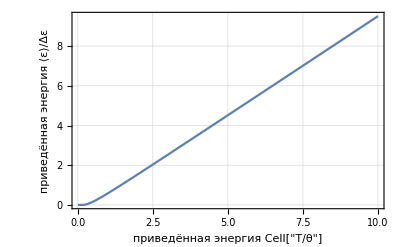

```mathematica
Plot[meanEHarm,{Tred,0.01,10},
PlotTheme->"Detailed",PlotLegends->None,
FrameLabel->{"приведённая энергия Cell["T/θ",ExpressionUUID->"fae0e510-7fc9-4e05-baf2-bc80f4e1ebc4"]","приведённая энергия ⟨ε⟩/Δε"}
]
```

## Система из n + 1 равномерно распределённых уровней

Переопределим выражение для энергии ε_n

```mathematica
ClearAll[ε]
Subscript[ε, i_]:=i ε
```

Тогда выражения для Q и P_n примут вид

```mathematica
Q=∑_(i=0)^n Exp[(-Subscript[ε, i])/(k T)]//FullSimplify
```

ⅇ^(-(5 ε)/(k T)) (1+2 Cosh[ε/(k T)]+2 Cosh[(2 ε)/(k T)]+2 Cosh[(3 ε)/(k T)]+2 Cosh[(4 ε)/(k T)]+2 Cosh[(5 ε)/(k T)])

```mathematica
populN=popul[i]//Simplify
```

ⅇ^(-((-5+i) ε)/(k T))/(1+2 Cosh[ε/(k T)]+2 Cosh[(2 ε)/(k T)]+2 Cosh[(3 ε)/(k T)]+2 Cosh[(4 ε)/(k T)]+2 Cosh[(5 ε)/(k T)])

Перейдём к приведённым координатам

```mathematica
populN=populN/.ε/(k T)->1/Tred
```

ⅇ^(-(-5+i)/Tred)/(1+2 Cosh[1/Tred]+2 Cosh[2/Tred]+2 Cosh[3/Tred]+2 Cosh[4/Tred]+2 Cosh[5/Tred])

### Пусть число уровней n = 5

```mathematica
n=5;
```

```mathematica
levelsN=Table[populN,{i,0,3}];
```

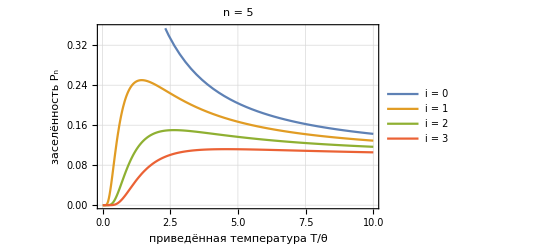

```mathematica
Plot[levelsN,{Tred,0.01,10},
PlotTheme->"Detailed",PlotLegends->Map[StringTemplate["i = ``"],Range[0,3]],
FrameLabel->{"приведённая температура T/θ","заселённость P_n"},
PlotLabel->"n = 5"
]
```

Найдём среднюю энергию

```mathematica
meanEN=∑_(i=0)^n populN Subscript[ε, i]//FullSimplify
```

((5+ⅇ^(1/Tred) (4+ⅇ^(1/Tred) (3+ⅇ^(1/Tred) (2+ⅇ^(1/Tred))))) ε)/(1+2 Cosh[1/Tred]+2 Cosh[2/Tred]+2 Cosh[3/Tred]+2 Cosh[4/Tred]+2 Cosh[5/Tred])

Перейдём к приведённым координатам

```mathematica
meanEN5=meanEN=meanEN/.ε->1
```

(5+ⅇ^(1/Tred) (4+ⅇ^(1/Tred) (3+ⅇ^(1/Tred) (2+ⅇ^(1/Tred)))))/(1+2 Cosh[1/Tred]+2 Cosh[2/Tred]+2 Cosh[3/Tred]+2 Cosh[4/Tred]+2 Cosh[5/Tred])

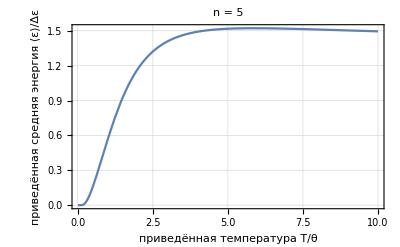

```mathematica
Plot[meanEN,{Tred,0.01,10},
PlotTheme->"Detailed",PlotLegends->None,
FrameLabel->{"приведённая температура T/θ","приведённая средняя энергия ⟨ε⟩/Δε"},
PlotLabel->"n = 5"
]
```

### Пусть число уровней n = 10

```mathematica
n=10;
```

```mathematica
levelsN=Table[populN,{i,0,3}]/.n->10;
```

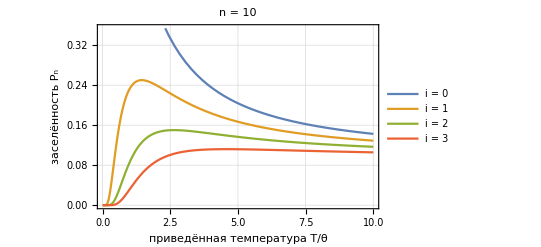

```mathematica
Plot[levelsN,{Tred,0.01,10},
PlotTheme->"Detailed",
PlotLegends->Map[StringTemplate["i = ``"],Range[0,3]],
FrameLabel->{"приведённая температура T/θ","заселённость P_n"},
PlotLabel->"n = 10"
]
```

```mathematica
meanEN=∑_(i=0)^n populN Subscript[ε, i]//FullSimplify
```

(ⅇ^(-5/Tred) (10+ⅇ^(1/Tred) (9+ⅇ^(1/Tred) (8+ⅇ^(1/Tred) (7+ⅇ^(1/Tred) (6+ⅇ^(1/Tred) (5+ⅇ^(1/Tred) (4+ⅇ^(1/Tred) (3+ⅇ^(1/Tred) (2+ⅇ^(1/Tred)))))))))) ε)/(1+2 Cosh[1/Tred]+2 Cosh[2/Tred]+2 Cosh[3/Tred]+2 Cosh[4/Tred]+2 Cosh[5/Tred])

Перейдём к приведённым координатам

```mathematica
meanEN10=meanEN=meanEN/.ε->1
```

(ⅇ^(-5/Tred) (10+ⅇ^(1/Tred) (9+ⅇ^(1/Tred) (8+ⅇ^(1/Tred) (7+ⅇ^(1/Tred) (6+ⅇ^(1/Tred) (5+ⅇ^(1/Tred) (4+ⅇ^(1/Tred) (3+ⅇ^(1/Tred) (2+ⅇ^(1/Tred)))))))))))/(1+2 Cosh[1/Tred]+2 Cosh[2/Tred]+2 Cosh[3/Tred]+2 Cosh[4/Tred]+2 Cosh[5/Tred])

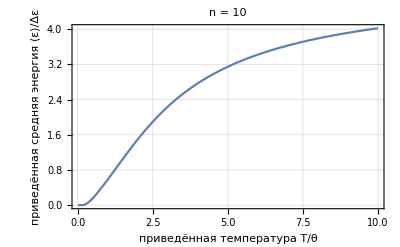

```mathematica
Off[General::munfl]
Plot[meanEN,{Tred,0.01,10},
PlotTheme->"Detailed",PlotLegends->None,
FrameLabel->{"приведённая температура T/θ","приведённая средняя энергия ⟨ε⟩/Δε"},
PlotLabel->"n = 10"
]
```

## Результаты

Изучена заселённость уровней P_i (как функции температуры) для двух систем: гармонического осциллятора и системы из n+1 равномерно распределённых уровней

Получены аналитические зависимости заселённостей P_i, их анализ показывает, что с ростом приведённой температуры T_red снижается заселённость нижних уровней в пользу более высоких

Средняя энергия системы из n + 1 уровней зависит от n, как и в статье [J. Chem. Educ. 2013, 90; Celestino Angeli et al.], были выбраны значения n = 5 и n = 10, средняя энергия монотонно растёт с увеличением температуры

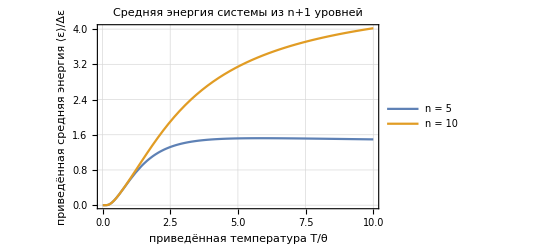

```mathematica
Plot[{meanEN5,meanEN10},{Tred,0.01,10},
PlotTheme->"Detailed",
FrameLabel->{"приведённая температура T/θ","приведённая средняя энергия ⟨ε⟩/Δε"},
PlotLegends->{"n = 5","n = 10"},
PlotLabel->"Средняя энергия системы из n+1 уровней"
]
```